```mathematica
H={{E0-d/2,3*e*a0},{3*e*a0,E0+d/2}}
```

{{-d/2+E0,3 a0 e},{3 a0 e,d/2+E0}}

```mathematica
Eigenvalues[H]//FullSimplify
```

{-1/2 √(d^2+36 a0^2 e^2)+E0,1/2 √(d^2+36 a0^2 e^2)+E0}

```mathematica
Eigensystem[H]
```

{{1/2 (-√(d^2+36 a0^2 e^2)+2 E0),1/2 (√(d^2+36 a0^2 e^2)+2 E0)},{{-(d+√(d^2+36 a0^2 e^2))/(6 a0 e),1},{-(d-√(d^2+36 a0^2 e^2))/(6 a0 e),1}}}

```mathematica
H=(d/2)*{{-1,Tan[t]},{Tan[t],+1}}
```

{{-d/2,1/2 d Tan[t]},{1/2 d Tan[t],d/2}}

```mathematica
H={{-w/2,V},{V,w/2}}
```

{{-w/2,V},{V,w/2}}

```mathematica
Eigensystem[H]//FullSimplify
```

{{-1/2 √(4 V^2+w^2),1/2 √(4 V^2+w^2)},{{-(w+√(4 V^2+w^2))/(2 V),1},{(-w+√(4 V^2+w^2))/(2 V),1}}}

```mathematica
(-1-1/Cos[t]) Cot[t]//FullSimplify
```

-Cot[t/2]

```mathematica
energy=hbar*Sqrt[(w0/2)^2+(3*e*a0*EField/hbar)^2];
```

```mathematica
Limit[D[energy,EField],{EField->Infinity}]//FullSimplify
```

3 √((a0^2 e^2)/hbar^2) hbar

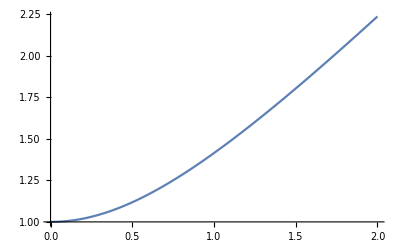

```mathematica
Plot[Sqrt[1+x^2],{x,0,2}]
```

```mathematica
Solve[2*(3*e*a0*EField)==w0*hbar,EField]
```

{{EField→(hbar w0)/(6 a0 e)}}

```mathematica
(1.06/2*1000)/21.77
```

24.3454